# Ph22 - Assignment 1

## Daniel Chica

## Problem 1

We can generalize the secant method as
x_(n+1)=x_n-f(x_n) (x_n-x_(n-1))/(f(x_n)-f(x_(n-1)))
Let’s suppose we are looking for the solution to f(x)=0, and we find f(ξ)=0, let’s define
x_n=ξ+ϵ_n
since this process is iterative, we know that as n→∞, x→ξ, which implies ϵ_∞→ 0, or the error is very small. Since we are looking for the order of convergence, this setup leads to the equation
x_(n+1)-ξ=(C(x_n-ξ))^r
which we can express in terms of the error as
ϵ_(n+1)=C ϵ_n^r
and our goal here is to solve for r.

Let’s plug in this new definition of x_n into the secant method
(ξ+ϵ_(n+1))=(ξ+ϵ_n)-f(ξ+ϵ_n) (ξ+ϵ_n-(ξ+ϵ_(n-1)))/(f(ξ+ϵ_n)-f(ξ+ϵ_(n-1)))
ϵ_(n+1)=ϵ_n-f(ξ+ϵ_n) (ϵ_n-ϵ_(n-1))/(f(ξ+ϵ_n)-f(ξ+ϵ_(n-1)))
Let’s expand the functions using a Taylor Expansion of order 2
f(ξ+ϵ_n)=f(ξ)+f'(ξ)ϵ_n+1/2 f''(ξ)ϵ_n^2
We know f(ξ)=0 from earlier, so
f(ξ+ϵ_n)=f'(ξ)ϵ_n+1/2 f''(ξ)ϵ_n^2
using a similar idea
f(ξ+ϵ_n)-f(ξ+ϵ_(n-1))=f'(ξ)ϵ_n+1/2 f''(ξ)ϵ_n^2-(f'(ξ)ϵ_(n-1)+1/2 f''(ξ)ϵ_(n-1)^2)=f'(ξ)(ϵ_n-ϵ_(n-1))+1/2 f''(ξ)(ϵ_n^2-ϵ_(n-1)^2)
making our secant method equation
ϵ_(n+1)=ϵ_n-(f'(ξ)ϵ_n+1/2 f''(ξ)ϵ_n^2)(ϵ_n-ϵ_(n-1))/(f'(ξ)(ϵ_n-ϵ_(n-1))+1/2 f''(ξ)(ϵ_n^2-ϵ_(n-1)^2))
let’s look at the fraction
(ϵ_n-ϵ_(n-1))/(f'(ξ)(ϵ_n-ϵ_(n-1))+1/2 f''(ξ)(ϵ_n^2-ϵ_(n-1)^2))=1/(f'(ξ)+1/2 f''(ξ)(ϵ_n^2-ϵ_(n-1)^2)/(ϵ_n-ϵ_(n-1)))=1/(f'(ξ))1/(1+1/2(f''(ξ))/(f'(ξ))(ϵ_n^2-ϵ_(n-1)^2)/(ϵ_n-ϵ_(n-1)))
Since the second term in the denominator is so small, we can take the approximation 1/(1+x)→ 1-x leading to
1/(f'(ξ))1/(1+1/2(f''(ξ))/(f'(ξ))(ϵ_n^2-ϵ_(n-1)^2)/(ϵ_n-ϵ_(n-1)))=1/(f'(ξ))(1-1/2(f''(ξ))/(f'(ξ))(ϵ_n^2-ϵ_(n-1)^2)/(ϵ_n-ϵ_(n-1)))
our recurrence relation becomes
ϵ_(n+1)=ϵ_n-(f'(ξ)ϵ_n+1/2 f''(ξ)ϵ_n^2)1/(f'(ξ))(1-1/2(f''(ξ))/(f'(ξ))(ϵ_n^2-ϵ_(n-1)^2)/(ϵ_n-ϵ_(n-1)))
ϵ_(n+1)=ϵ_n-(ϵ_n+1/2(f''(ξ))/(f'(ξ))ϵ_n^2)(1-1/2(f''(ξ))/(f'(ξ))(ϵ_n^2-ϵ_(n-1)^2)/(ϵ_n-ϵ_(n-1)))
ϵ_(n+1)= (1/2(f''(ξ))/(f'(ξ)))^2 ϵ_n^3+(1/2(f''(ξ))/(f'(ξ)))ϵ_n ϵ_(n-1) +(1/2(f''(ξ))/(f'(ξ)))^2 ϵ_n^2 ϵ_(n-1)
We can neglect the first and third terms since ϵ^3 will be very small and thus negligible, leaving
ϵ_(n+1)≈(1/2(f''(ξ))/(f'(ξ)))ϵ_n ϵ_(n-1)
we can now change the LHS and solve
C ϵ_n^r=(1/2(f''(ξ))/(f'(ξ)))ϵ_n ϵ_(n-1)→ ϵ_n^r/ϵ_n=1/C(1/2(f''(ξ))/(f'(ξ)))ϵ_(n-1)
 ϵ_n^(r-1)=1/C(1/2(f''(ξ))/(f'(ξ)))ϵ_(n-1)→ ϵ_n=(1/(2C)(f''(ξ))/(f'(ξ)))^(1/(r-1))ϵ_(n-1)^(1/(r-1))
Once again, we can plug in the LHS leading to
 Cϵ_(n-1)^r=(1/(2C)(f''(ξ))/(f'(ξ)))^(1/(r-1))ϵ_(n-1)^(1/(r-1))
This implies then
C=(1/(2C)(f''(ξ))/(f'(ξ)))^(1/(r-1))
r=1/(r-1)
We know the order of convergence must be a positive number, so solving for r yields,
r(r-1)=1
r^2-r-1=0
r=(-(-1)+√(1-4(1)(-1)))/2=(1+√5)/2=1.61803
so the order of convergence is the Golden Ratio, r=ϕ=1.618

## Problem 2

## Problem 3

x =a(Cos[ξ] -e)
y = a √(1-e^2)Sin[ξ] 
t = T/(2π)(ξ-e Sin[ξ])

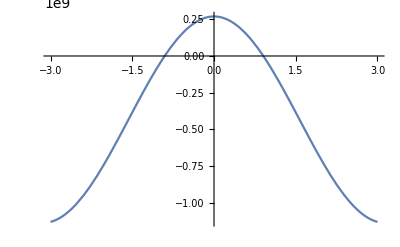

```mathematica
e=0.617139;
T=27906.98161;
a=2.34186*3*10^8;
Plot[ a(Cos[ξ]-e),{ξ,-3,3}]
```